```mathematica
UG=Import["C:\\fpgithub\\0908-LHWZ\\data\\02_Uran_Untergrund_1000-4000-100.txt","Table"];
U=Import["C:\\fpgithub\\0908-LHWZ\\data\\01_Uran_Zaehlrohrcharakteristik_1000-4000-100.txt","Table"];Smkl=Import["C:\\fpgithub\\0908-LHWZ\\data\\03_Sm_grFl_Zaehlrohrcharakteristik_1000-2200-100.txt","Table"];Smm=Import["C:\\fpgithub\\0908-LHWZ\\data\\05_Sm_klFL_Zaehlrohrcharakteristik_1000-2200-100.txt","Table"];Smgr=Import["C:\\fpgithub\\0908-LHWZ\\data\\07_Sm_ggrFl_Zaehlrohrcharakteristik_1000-2200-100.txt","Table"];
```

```mathematica
UG
U
Smkl
Smm
Smgr
```

{{1000000,0},{1100000,20},{1200000,140},{1300000,20},{1400000,0},{1500000,0},{1600000,0},{1700000,0},{1800000,40},{1900000,40},{2000000,0},{2100000,80},{2200000,100},{2300000,100},{2400000,300},{2500000,200},{2600000,300},{2700000,520},{2800000,540},{2900000,440},{3000000,600},{3100000,840},{3200000,760},{3300000,740},{3400000,720},{3500000,1220},{3600000,880},{3700000,3480},{3800000,3040},{3900000,8520},{4000000,6420}}

{{1000000,26440},{1100000,26860},{1200000,27960},{1300000,28340},{1400000,28880},{1500000,26860},{1600000,29400},{1700000,30040},{1800000,30280},{1900000,31120},{2000000,34740},{2100000,43260},{2200000,59240},{2300000,87720},{2400000,140020},{2500000,240820},{2600000,403860},{2700000,599460},{2800000,716180},{2900000,769680},{3000000,816140},{3100000,828200},{3200000,836760},{3300000,859120},{3400000,878860},{3500000,952020},{3600000,1077080},{3700000,1380220},{3800000,1839900},{3900000,2308700},{4000000,2768040}}

{{1000000,300},{1100000,160},{1200000,140},{1300000,200},{1400000,140},{1500000,320},{1600000,100},{1700000,140},{1800000,200},{1900000,360},{2000000,260},{2100000,340},{2200000,400}}

{{1000000,120},{1100000,220},{1200000,340},{1300000,300},{1400000,360},{1500000,180},{1600000,120},{1700000,120},{1800000,500},{1900000,360},{2000000,380},{2100000,280},{2200000,880}}

{{1000000,320},{1100000,720},{1200000,480},{1300000,600},{1400000,580},{1500000,760},{1600000,860},{1700000,720},{1800000,800},{1900000,800},{2000000,940},{2100000,1080},{2200000,900}}

```mathematica
Smgr[[All,2]]
Mean[Smgr[[All,2]]]//N
```

{320,720,480,600,580,760,860,720,800,800,940,1080,900}

735.385

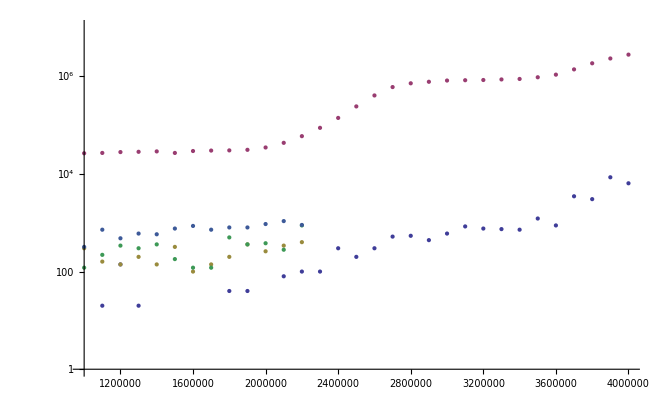

```mathematica
ListLogPlot[{UG,U,Smkl,Smm,Smgr},PlotRange->{1,10^7}]
```